```mathematica
(* Lecture 6: Graphic functions. Dynamics. Controls (Google's Version) *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,VectorPlot, VectorPlot3D,StreamPlot,RevolutionPlot3D,ContourPlot3D, Graphics3D}, ImageSize->Medium];
```

```mathematica
(* Explicit and parametric surface
    s1[x_,y_,n_]:=n*(x^2 + y^2)/10 
and a parametric surface  
xp1[u_,v_,n_]:=(3 + Cos[v]) Sin[u]+Cos[n v]
      yp1[u_,v_]:=(3 + Cos[v]) Cos[u]
      zp1[v_]:=Sin[v] the animation parameter {n,1,5,0.1}
{x,-4,4},{y,-4,4}{u,-4,4},v,-4,4} PlotPoints->40, *)
```

```mathematica
(* Define *)
```

```mathematica
sE1[x_,y_,n_]:=n*(x^2 + y^2)/10
```

```mathematica
xp1[u_,v_,n_]:=(3 + Cos[v]) Sin[u]+Cos[n v]
```

```mathematica
yp1[u_,v_]:=(3 + Cos[v]) Cos[u]
```

```mathematica
zp1[v_]:=  Sin[v]
```

```mathematica
sP1[u_,v_,n_]:={xp1[u,v,n],yp1[u,v] ,zp1[v]}
```

```mathematica
(* Define and check the graphics functions *)
```

```mathematica
PlotE1[n_]:=Plot3D[sE1[x,y,n],{x,-4,4},{y,-4,4},PlotStyle->Blue,Mesh->True, MeshStyle->Yellow]
```

```mathematica
PlotP1[n_]:=ParametricPlot3D[sP1[u,v,n],{u,-4,4},{v,-4,4},PlotStyle->Red]
```

```mathematica
(* Check *)
```

```mathematica
{PlotE1[1],PlotP1[3]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
(* Combine by Show[] *)
```

```mathematica
Plot1[n_]:=Show[{PlotE1[n],PlotP1[n]},PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}}]
```

```mathematica
(* Animation (improve the graph in class*)
```

```mathematica
Manipulate[Plot1[n],{n,1,5,0.5}]
```

```mathematica
(* Animate surface of revolution. The base function is given by 
{Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5}
{t,0,Pi} {n,1,7,0.5}*)
```

```mathematica
(* Check *)
```

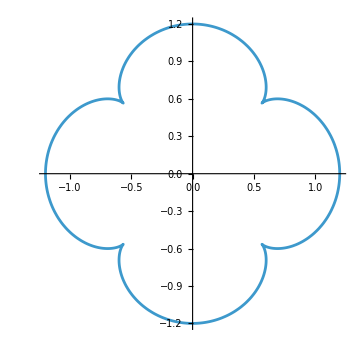

```mathematica
ParametricPlot[{Sin[t]+Sin[5 t]/5,Cos[t]+Cos[5 t]/5},{t,0,2Pi}]
```

```mathematica
G2[n_]:=RevolutionPlot3D[{Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5},{t,0,Pi},PlotRange->1.5,Mesh->True]
```

```mathematica
Manipulate[G2[n],{n,1,10,0.5}]
```

```mathematica
(* Manipulate. Fix the PlotRange by yourself (I have fixed it!) *)
```

```mathematica
Manipulate[G3All[t],{t,0,2Pi,0.05}]
```

```mathematica
(* Animate Graphics3D Animate a Sphere a Cube and Cylinder (any size) moving along a trajectory given by a circle with the R=5 in the x,y-plane 
 *)
```

```mathematica
(* Circle  in 3D for z=0 (the (x,y)-plane) *)
```

```mathematica
R=5;
```

```mathematica
x3[t_]:=R Cos[t]
```

```mathematica
y3[t_]:=R Sin[t]
```

```mathematica
z3[t_]:=0
```

```mathematica
C3[t_]:={x3[t],y3[t],z3[t]}
```

```mathematica
GC3=ParametricPlot3D[C3[t],{t,0,2Pi},BoxRatios->{1, 1, 0.5}]
```

-Graphics3D-

```mathematica
G3[t_]:=Graphics3D[Sphere[C3[t]]]
```

```mathematica
G3All[t_]:=Show[G3[t],GC3,PlotRange->{{-6,6},{-6,6},{-2,2}}]
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* -Graphics-*)
```

```mathematica
(* Cylinder *)
```

```mathematica
Graphics3D[Cylinder[{{1,1,2},{1,1,3}},2 ],Axes->True,AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

```mathematica
(* A bit different definition of the cylinder  *)
```

```mathematica
RCyl=1.5; (* Rad *)
```

```mathematica
h=1;  (* height *)
```

```mathematica
(* Axis of the cylinder -> 3D vector1-3D vector2  *)
```

```mathematica
hcyl={0,0,h/2};
```

```mathematica
CLine[t_]:={C3[t]+hcyl,C3[t]-hcyl};
```

```mathematica
(* Analyze every element of the animation *)
```

```mathematica
G3Obj3[t_]:=Graphics3D[{{Sphere[C3[t]]},{Opacity[0.7],Green, Cylinder[{CLine[t+0.5]},RCyl]},{Thick,Line[CLine[t+0.5]]},{Red, Cube[C3[t+1],RC ]}}]
```

```mathematica
(* Cylinder  *)
```

```mathematica
RC=1;
```

```mathematica
Graphics3D[Cube[{1,1,2},RC ],Axes->True,AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

```mathematica
(* Check *)
```

```mathematica
G3Obj3[1]
```

-Graphics3D-

```mathematica
(* Decompose into the graphic functions and Animate *)
```

```mathematica
myS[t_]:={Sphere[C3[t]]}
```

```mathematica
myCyl[t_]:={Opacity[0.7],Green, Cylinder[{CLine[t+0.5]},RCyl]}
```

```mathematica
myLine[t_]:={Thick,Line[CLine[t+0.5]]}
```

```mathematica
myCube[t_]:={Red, Cube[C3[t+1],RC ]}
```

```mathematica
myG3[t_]:=Graphics3D[{myS[t],myCyl[t],myLine[t],myCube[t]}]
```

```mathematica
myG3[1]
```

-Graphics3D-

```mathematica
S3All[t_]:=Show[{GC3,myG3[t]},ImageSize->Medium,PlotRange->6]
```

```mathematica
S3AllNew[t_]:=Show[{GC3,myG3[t]},PlotRange->{{-6,6},{-6,6},{-2,2}}]
```

```mathematica
(* Animate *)
```

```mathematica
Manipulate[S3AllNew[t],{t,0,12Pi}]
```

```mathematica
(* Move the cube in the opposite direction *)
```

```mathematica
G3Cube[t_]:=Graphics3D[{myS[t],myCyl[t],myLine[t],myCube[-t]}]
```

```mathematica
S3Cube [t_]:=Show[{GC3,G3Cube[t]},PlotRange->{{-6,6},{-6,6},{-2,2}}]
```

```mathematica
Manipulate[S3Cube[t],{t,0,12Pi}]
```

```mathematica
(* Sliders and Dynamics *)
```

```mathematica
(* An ordinary Mathematica session consists of a series of static inputs and outputs which forms a record of calculations done in the order in which they were executed. However you may often want a fundamentally different kind of output. The one that is automatically updated to always reflect its current value. This new kind of output is provided by the function Dynamic *)
```

```mathematica
(* Compare *)
```

```mathematica
x=68
```

68

```mathematica
(* and *)
```

```mathematica
Dynamic[x]
```

```mathematica
Dynamic[x^2]
```

```mathematica
x
```

68

```mathematica
(* Slider changes the variable dynamically *)
```

```mathematica
{Slider[Dynamic[s],{-4,75,3}] ,Dynamic[s]}
```

{,}

```mathematica
s
```

26

```mathematica
(* Dynamic[s] makes the output interactive  *)
```

```mathematica
Dynamic[s]
```

```mathematica
(* The slider below changes "n" from 0 to 100 with the step 2. We also output the Dynamic[n] in the same line using { } *)
```

```mathematica
{Slider[Dynamic[n],{0,100,1}],Dynamic[n]} (* var ใน slider ต้องเป็น dynamic / หลัง , เป็น output ให้โชว์เฉย ๆ *)
```

{,}

```mathematica
(* Dynamic graphics. The plot depends on the dynamic variable assigned after the plot is executed  *)
```

```mathematica
a=3;
```

```mathematica
f[x_,a_]:=a*x^2
```

```mathematica
{Dynamic[Plot[f[x,a],{x,-1,1},PlotRange->{{-1,1},{0,10}}]],{Slider[Dynamic[a],{0,10,1},Background->LightBlue],Dynamic[a]}}
```

{,{,}}

```mathematica
(* Use the slider to animate (x-1/n5)^2+y^2 
where R1 is the animation variable changing from 1 to 20 with the step 1. Fix the PlotRange  *)
```

```mathematica
f5[x_,y_,n5_]:=(x-1/n5)^2+y^2
```

```mathematica
P5[n5_]:=Plot3D[f5[x,y,n5],{x,-1,1},{y,-1,1},PlotRange->{Automatic,Automatic,{0,5}}]
```

```mathematica
{Dynamic[P5[n5]],Slider[Dynamic[n5], {1,20,1}],Dynamic[n5]}
```

{,,}

```mathematica
(* Animate Sin[n6*x]*Exp[-y^2*m6] with 2 sliders m6 and n6 changing from 0 to 10 with step 1 {x,-1,1} {y,-1,1} The sliders and the graph are combined *)
```

```mathematica
f6[x_,y_,n6_,m6_]:=Sin[n6*x]*Exp[-y^2*m6]
```

```mathematica
P6[n6_,m6_]:=Plot3D[f6[x,y,n6,m6],
{x,-1,1} ,{y,-1,1},PlotStyle->Red,PlotRange->1]
```

```mathematica
(* Slider-"functions" *)
```

```mathematica
Sm6:={Slider[Dynamic[m6],{0,10,1},Background->LightBlue],Dynamic[m6]}
```

```mathematica
Sn6:={Slider[Dynamic[n6],{0,10,1},Background->Green],Dynamic[n6]}
```

```mathematica
{Dynamic[P6[n6,m6]],Sm6,Sn6}
```

{,{,},{,}}

```mathematica
(*  ContourPlot3D displays 3D contours of a 4D surface f[x_,y_,z_] *)
```

```mathematica
f7[x_,y_,z_]:=x y z
```

```mathematica
(* Contours *)
```

```mathematica
TC7:={ -2,1,0,1,2}
```

```mathematica
ContourPlot3D[f7[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->TC7,ContourStyle ->Opacity[0.5]]
```

-Graphics3D-

```mathematica
(* Unlike ContourPlot ContourPlot3D does not display the value of the function as we move the mouse over the contours. Nor can we display those values with the ContourLabels which is no longer an allowable option. We are on our own here to understand what we are looking at! The line below shows how to plot a single contour f=1 using Contours->{0.1} *)
```

```mathematica
ContourPlot3D[f7[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{0.1},ContourStyle ->Opacity[0.8]]
```

-Graphics3D-

```mathematica
(* Sliders allow to control the 4D contours *)
```

```mathematica
(* Change the contour-surfaces from f=0 to f=3 with a certain step (some parts of the examples with f7 might be omitted) *)
```

```mathematica
(* Slider- "function" *)
```

```mathematica
MySlider7:={Slider[Dynamic[c],{0,3,0.5}],Dynamic[c]}
```

```mathematica
(* Graphic function  *)
```

```mathematica
Plot7[c_]:=ContourPlot3D[f7[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{c},ContourStyle ->Opacity[ 0.8]]
```

```mathematica
(* Animation  *)
```

```mathematica
{MySlider7,Dynamic[Plot7[c]]}
```

{{,},}

```mathematica
(* Vertical Slider  *)
```

```mathematica
MySlider7V:={VerticalSlider[Dynamic[cv],{0,3,0.1},Background->Yellow],Dynamic[cv]}
```

```mathematica
{MySlider7V,Dynamic[Plot7[cv]]}
```

{{,},}

```mathematica
(* Toggler *)
```

```mathematica
(* Toggler dynamically updates the output from a given list when the output gets clicked *)
```

```mathematica
TL7=Table[0.5i,{i,10}]
```

{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
Toggler[Dynamic[a],TL7,Background->Blue,BaseStyle->White]
```

```mathematica
Dynamic[a]
```

```mathematica
(* Animate plot7[c] using the Toggler. *)
```

```mathematica
MyToggler7:=Toggler[Dynamic[c],TL7,Background->Blue,BaseStyle->White]
```

```mathematica
{MyToggler7,Dynamic[Plot7[c]]}
```

{,}

```mathematica
(* Modify the Opacity of the ContourPlot3D[f7[x,y,z],] 
op={0.1,0.2,0.3,0.4.0.5,0.75,0.9,1.0} using Toggler *)
```

```mathematica
Plot7o[op_]:=ContourPlot3D[f7[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{1},ContourStyle ->Opacity[op],Mesh-> False,ImageSize->Small]
```

```mathematica
T7o={0.1,0.2,0.3,0.5,0.75,0.9,1.0}
```

{0.1,0.2,0.3,0.5,0.75,0.9,1.}

```mathematica
MyToggler7o:=Toggler[Dynamic[op],T7o,Background->Blue,BaseStyle->White]
```

```mathematica
{MyToggler7o,Dynamic[Plot7o[op]]}
```

{,}

```mathematica
(* Setup a Toggler to change the number of contours c1={2,4,6,8,10,12,14}*)
```

```mathematica
T7n= Table[2i,{i,1,7}]
```

{2,4,6,8,10,12,14}

```mathematica
MyToggler7n:=Toggler[Dynamic[c1],T7n,Background->Pink,BaseStyle->Black]
```

```mathematica
plot7n[c1_]:=ContourPlot3D[f7[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->c1,ContourStyle ->Opacity[0.8]]
```

```mathematica
{Dynamic[plot7n[c1]],MyToggler7n}
```

{,}

```mathematica
(* Radio button Bar for plot51[c1] *)
```

```mathematica
RBar7:=RadioButtonBar[Dynamic[c1],T7n,Background->Purple]
```

```mathematica
{Dynamic[plot7n[c1]],RBar7}
```

{, | 2   | 4   | 6   | 8   | 10   | 12   | 14}

```mathematica
(* Combination of Manipulate and Toggler Animate Sin[k1 x y]*Exp[k2*(x^2-y^2)] where k1 is a Toggler {1,3,5,6} and k2 is the animation parameter from -5 to 5 with step 0.1
Fix the PlotRange *)
```

```mathematica
f8[x_,y_,k1_,k2_]:=Sin[k1*x*y]*Exp[-0.1k2(x^2-y^2)]
```

```mathematica
Toggler8:=Toggler[Dynamic[k1],{1,3,5,6},Background->Black,BaseStyle->White]
```

```mathematica
plot8[k1_,k2_]:=Plot3D[f8[x,y,k1,k2],{x,-1,1},{y,-1,1},PlotRange->1.5]
```

```mathematica
Toggler8
```

```mathematica
Manipulate[plot8[k1,k2],{k2,-5,5,0.1}]
```

```mathematica
(* Compare: Toggler inside Manipulate *)
```

```mathematica
Manipulate[{plot8[k1,k2],Toggler8},{k2,-5,5,0.1}]
```

```mathematica
(* Compare: Manipulate with 2 parameters *)
```

```mathematica
Manipulate[plot8[k1,k2],{k1,{1,3,5,6}},{k2,-5,5,0.1}]
```

```mathematica
(* Manipulate with 3 parameters *)
```

```mathematica
ColorList8={Red,Green,Blue,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5]}

```mathematica
(* Incude the new variable C. Check different style of the controls *)
```

```mathematica
plot82[k1_,k2_,C_]:=Plot3D[f8[x,y,k1,k2],{x,-1,1},{y,-1,1},PlotStyle->C,PlotRange->1.5]
```

```mathematica
Manipulate[plot82[k1,k2,C],{k1,{1,3,5,6}},{k2,-5,5,0.1},{C,ColorList8}]
```

```mathematica
PopupMenu[Dynamic[m9],{1,2,3}]
```

```mathematica
Dynamic[m9]
```

```mathematica
PopupMenu[Dynamic[mm9],{1->"0ne",2->"Two",3->"anything"}]
```

```mathematica
Dynamic[mm9]
```

```mathematica
(* Animate f6, k1=2 and k2=3. The color is updated by the PopupMenu*)
```

```mathematica
PopMenu9:=PopupMenu[Dynamic[color9],{Red,Green ,Blue,Purple,Pink,LightBlue}]
```

```mathematica
P9[color_]:=Plot3D[f8[x,y,2,3],{x,-1,1},{y,-1,1}, PlotStyle->color]
```

```mathematica
{Dynamic[P9[color9] ],PopMenu9}
```

{,}

```mathematica
(* A menu with textual items *)
```

```mathematica
PopMenu101:=PopupMenu[Dynamic[color101], {Red->"Red",Green->"Green" ,Blue->"Blue",Purple->"Purple",Pink->"Pink"}]
```

```mathematica
plot101[color2_]:=Plot3D[f6[x,y,2,3],{x,-1,1},{y,-1,1}, PlotStyle->color2]
```

```mathematica
{Dynamic[plot101[color101]],PopMenu101}
```

{,}

```mathematica
(* Setter Bar *)
```

```mathematica
SB11:=SetterBar[Dynamic[color11],{Red,Green,Blue,Purple,Black,Yellow,Orange,Cyan}]
```

```mathematica
{Dynamic[plot101[color11]],SB11}
```

{, |  |  |  |  |  |  | }

```mathematica
(* Move a sphere R=3 along the spiral with the radius 12. Control the color using ColorSider use graphics 3D *)
```

```mathematica
(* Spiral *)
```

```mathematica
RSp=12
```

12

```mathematica
(* Sphere *)
```

```mathematica
RS=3
```

3

```mathematica
x12[t_]:=RSp Cos[t]
```

```mathematica
y12[t_]:=RSp Sin[t]
```

```mathematica
z12[t_]:=t
```

```mathematica
(* Spiral *)
```

```mathematica
Spiral12[t_]:={x12[t],y12[t],z12[t]}
```

```mathematica
(* Graphics 3D *)
```

```mathematica
(* Sphere *)
```

```mathematica
GSphere12[t_]:=Graphics3D[{color12,Sphere[Spiral12[t],RS]}]
```

```mathematica
(* ColorSlider *)
```

```mathematica
CS12=ColorSlider[Dynamic[color12]]
```

$CellContext`color12

```mathematica
(* Check *)
```

```mathematica
Dynamic[GSphere12[1]]
```

```mathematica
(* Spiral *)
```

```mathematica
GSpiral12=ParametricPlot3D[Spiral12[t],{t,0,24},PlotRange->{{-16,16},{-16,16},{0,20}}]
```

-Graphics3D-

```mathematica
(* Show, Dynamic *)
```

```mathematica
GAll12[t_]:=Dynamic[Show[{GSpiral12,GSphere12[t]},Axes->True]]
```

```mathematica
(* Check *)
```

```mathematica
GAll12[3]
```

```mathematica
(* Animate. The slider has been included into Manipulate*)
```

```mathematica
Manipulate[{GAll12[t],CS12},{t,1,24,0.01}]
```

```mathematica
(* Compare. Use the parametric equations of the sphere instead of Graphics 3D to solve the problem above. The equations of the sphere at {x,y,z} with the radius R are 
{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{v,0,2*Pi},{u,-Pi/2,Pi/2}
*)
```

```mathematica
RS=3;
```

```mathematica
x13[u_,v_]:=Cos[v]*Cos[u]
```

```mathematica
y13[u_,v_]:= Sin[v]*Cos[u]
```

```mathematica
z13[u_,v_]:= Sin[u]
```

```mathematica
sphere[u_,v_]:=RS{x13[u,v],y13[u,v],z13[u,v]}
```

```mathematica
(* Move sphere[u_,v_] to P={x,y,z} *)
```

```mathematica
color12=Blue;
```

```mathematica
spheremove[u_,v_,P_]:=sphere[u,v]+P
```

```mathematica
(* Check! *)
```

```mathematica
spheremove[1.,1,Spiral12[Pi]];
```

```mathematica
(* It works!  Hence*)
```

```mathematica
GspMove[t_]:=ParametricPlot3D[spheremove[u,v,Spiral12[t]],{u,0,2Pi},{v,0,Pi},PlotStyle->color12,PlotPoints->35,Mesh->None]
```

```mathematica
(* Check! *)
```

```mathematica
GspMove[2]
```

-Graphics3D-

```mathematica
(* Beautiful! We have *)
```

```mathematica
Spiral12[1.]
```

{6.48363,10.0977,1.}

```mathematica
(* Plot *)
```

```mathematica
GSpiral12
```

-Graphics3D-

```mathematica
(* Show, Dynamic *)
```

```mathematica
GAll13[t_]:=Dynamic[Show[GSpiral12,GspMove[t]]]
```

```mathematica
(* Check *)
```

```mathematica
GAll13[10]
```

```mathematica
(* Animate *)
```

```mathematica
Manipulate[{GAll13[t],CS12},{t,1,12}]
```